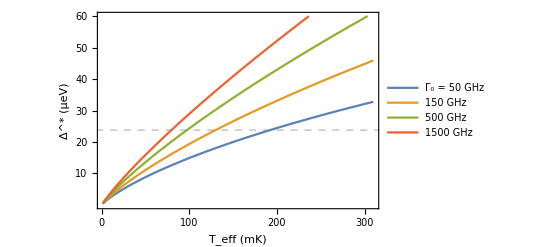

```mathematica
(*---Unit conversions---*)GHzToMicroeV=4.13567;
GHzToMilliK=48.0;

(*---Clear symbols---*)
ClearAll[myDelta,mykT,myGamma0]

(*---Piecewise equation---*)
eq[mykT_?NumericQ,myDelta_,myGamma0_?NumericQ]:=Piecewise[{{2 myDelta/mykT-Log[myGamma0/mykT]==mykT/(2 myDelta),mykT<myGamma0},{2 myDelta/mykT==mykT/(2 myDelta),mykT>=myGamma0}}];

(*---Solve for positive root---*)
deltaSol[mykT_?NumericQ,myGamma0_?NumericQ]:=myDelta/. FindRoot[eq[mykT,myDelta,myGamma0],{myDelta,1}];

(*---Convert to physical units---*)
deltaPhysical[TmK_?NumericQ,gamma0GHz_?NumericQ]:=Module[{kTGHz,deltaGHz},(*Convert temperature to GHz*)kTGHz=TmK/GHzToMilliK;
(*Solve equation*)deltaGHz=deltaSol[kTGHz,gamma0GHz];
(*Convert result to micro-eV*)GHzToMicroeV*deltaGHz]

(*---Plot---*)
Plot[Evaluate@Table[deltaPhysical[T,g0],{g0,{50,150,500,1500}}],{T,1,310},(*temperature in mK*)Axes->False,Frame->True,FrameStyle->Black,BaseStyle->{FontSize->14,FontFamily->"Helvetica"},FrameLabel->{"\!\(\*SubscriptBox[\(T\), \(eff\)]\) (mK)","\!\(\*SuperscriptBox[\(Δ\), \(*\)]\) (μeV)",None,None},PlotRange->{{1,310},{0,60}},
(*---Custom ticks---*)FrameTicks->{{{10,20,30,40,50,60},None},(*y-axis*){{0,100,200,300},None}    (*x-axis*)},
(*---Horizontal reference line---*)GridLines->{None,{23.8}},GridLinesStyle->Directive[Thick,Gray,Dashed],
(*---Legend---*)PlotLegends->{"\!\(\*SubscriptBox[\(Γ\), \(0\)]\) = 50 GHz","150 GHz","500 GHz","1500 GHz"}]
```